```mathematica
Clear[v,g,eps,ky,k2list,k2];
k0 =Sqrt[1-eps^2];
g[v_] = 1+eps*Sin[v];
gp[v_] = D[g[v],v];
gpp[v_] = D[D[g[v],v],v];
v0p[v_] = -g[v]/k0;
v0pp[v_] = D[v0p[v],v]*v0p[v];
v0ppp[v_]=D[v0pp[v],v]*v0p[v];
v1[v_] = ((k0^2+ky^2)/k0)*(v0p[v]*Log[-v0p[v]]);
v1p[v_] = D[v1[v],v]*v0p[v];
v1pp[v_]=D[v1p[v],v]*v0p[v];
```

```mathematica
(*eps = 3/10;
k2list = {};
ky = 0.2;
inner1 = -2*k0*(k0^2+ky^2)*NIntegrate[v0ppp[v]/v0p[v]^2,{v,Pi,-Pi}];
inner2 = (k0^2+ky^2)*NIntegrate[v1pp[v]/v0p[v]^2,{v,Pi,-Pi}];
inner3 = -1*NIntegrate[gpp[v]*(v1[v])^2/v0p[v]^2,{v,Pi,-Pi}];
k2 = (inner1+inner2+inner3)/(2*Pi);*)

(*For[ky=0.96542,ky<0.96544,ky+=0.000001, 
inner1 = -2*k0*(k0^2+ky^2)*NIntegrate[v0ppp[v]/v0p[v]^2,{v,Pi,-Pi}];
inner2 = (k0^2+ky^2)*NIntegrate[v1pp[v]/v0p[v]^2,{v,Pi,-Pi}];
inner3 = -1*NIntegrate[gpp[v]*(v1[v])^2/v0p[v]^2,{v,Pi,-Pi}];
k2 = (inner1+inner2+inner3)/(2*Pi);
AppendTo[k2list,{ky,k2}];
];*)

plotlist = {};
eps=1/10;
k2[ky_] = (-2*k0*(k0^2+ky^2)*NIntegrate[v0ppp[v]/v0p[v]^2,{v,Pi,-Pi}]+(k0^2+ky^2)*NIntegrate[v1pp[v]/v0p[v]^2,{v,Pi,-Pi}]+-1*NIntegrate[gpp[v]*(v1[v])^2/v0p[v]^2,{v,Pi,-Pi}])/(2*Pi);
AppendTo[plotlist,Plot[k2[ky],{ky,0.0,1.8},PlotStyle-> Blue,PlotRange->{-0.2,1}]];

eps=3/10;
k2[ky_] = (-2*k0*(k0^2+ky^2)*NIntegrate[v0ppp[v]/v0p[v]^2,{v,Pi,-Pi}]+(k0^2+ky^2)*NIntegrate[v1pp[v]/v0p[v]^2,{v,Pi,-Pi}]+-1*NIntegrate[gpp[v]*(v1[v])^2/v0p[v]^2,{v,Pi,-Pi}])/(2*Pi);
AppendTo[plotlist,Plot[k2[ky],{ky,0.0,1.8},PlotStyle-> Red,PlotRange->{-0.2,1}]];

eps=5/10;
k2[ky_] = (-2*k0*(k0^2+ky^2)*NIntegrate[v0ppp[v]/v0p[v]^2,{v,Pi,-Pi}]+(k0^2+ky^2)*NIntegrate[v1pp[v]/v0p[v]^2,{v,Pi,-Pi}]+-1*NIntegrate[gpp[v]*(v1[v])^2/v0p[v]^2,{v,Pi,-Pi}])/(2*Pi);
AppendTo[plotlist,Plot[k2[ky],{ky,0.0,1.8},PlotStyle-> Green,PlotRange->{-0.2,1}]];

eps=7/10;
k2[ky_] = (-2*k0*(k0^2+ky^2)*NIntegrate[v0ppp[v]/v0p[v]^2,{v,Pi,-Pi}]+(k0^2+ky^2)*NIntegrate[v1pp[v]/v0p[v]^2,{v,Pi,-Pi}]+-1*NIntegrate[gpp[v]*(v1[v])^2/v0p[v]^2,{v,Pi,-Pi}])/(2*Pi);
AppendTo[plotlist,Plot[k2[ky],{ky,0.0,1.8},PlotStyle-> Black,PlotRange->{-0.2,1}]];

eps=9/10;
k2[ky_] = (-2*k0*(k0^2+ky^2)*NIntegrate[v0ppp[v]/v0p[v]^2,{v,Pi,-Pi}]+(k0^2+ky^2)*NIntegrate[v1pp[v]/v0p[v]^2,{v,Pi,-Pi}]+-1*NIntegrate[gpp[v]*(v1[v])^2/v0p[v]^2,{v,Pi,-Pi}])/(2*Pi);
AppendTo[plotlist,Plot[k2[ky],{ky,0.0,1.8},PlotStyle-> Pink,PlotRange->{-0.2,1}]];
```

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
k=k0+k2/(cx^2);
```

```mathematica
NumberForm[k2,20];
```

```mathematica
(*NumberForm[FindRoot[k2[ky],{ky,1}],20]*)
```

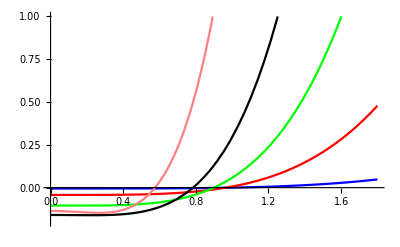

```mathematica
Show[plotlist[[1]],plotlist[[2]],plotlist[[3]],plotlist[[4]],plotlist[[5]]]
```